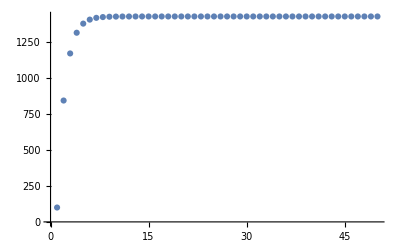

On the 2nd day, 844 students are infected and 4156 are healthy.

On the 10th day, 1428 students are infected and 3572 are healthy.

The number of cases will have stabilized by the 10th day, assuming a change of less than 1 person per day is stable.

To have 1400 infected on the third day, there would need to be 1281 infected students and 3719 healthy students at the start of the epidemic.

```mathematica
transition={{.6,.16},{.4,.84}};
population={100,4900};
iData = {};
iRate = {};
firstCaseCheckDay = 2;
secondCaseCheckDay = 10;

For[i=1,i<=50,prior = population;
AppendTo[iData,{i,population[[1]]}];
If[i==firstCaseCheckDay ,firstCheck=population];
If[i==secondCaseCheckDay,secondCheck=population];
population = transition.population;
AppendTo[iRate,population[[1]]-prior[[1]]];
i++];

ListPlot[iData,PlotRange->All]
Print[StringForm["On the ``nd day, `` students are infected and `` are healthy.",
firstCaseCheckDay,
Round[firstCheck[[1]]],
Round[firstCheck[[2]]]]]
Print[StringForm["On the ``th day, `` students are infected and `` are healthy.",
secondCaseCheckDay,
Round[secondCheck[[1]]],
Round[secondCheck[[2]]]]]
Print[StringForm[
"The number of cases will have stabilized by the ``th day, assuming a change of less than 1 person per day is stable.",
FirstPosition[iRate,x_/;x<1][[1]]]];

thirdDayTransition =transition.transition;
thirdDayPopulation = {1400, 3600};
startingPopulation=Inverse[thirdDayTransition].thirdDayPopulation;
Print[StringForm[
"To have 1400 infected on the third day, there would need to be `` infected students and `` healthy students at the start of the epidemic.",
Round[startingPopulation[[1]]],
Round[startingPopulation[[2]]] ]]
```